```mathematica
{{Needs["PacletManager`"]
PacletInstall["Wolfram Mathematica/IGraphM-0.6.5.paclet"]
Needs["IGraphM`"]

G = Import["Grafencollectie\\r44_15.g6"];
Len=Min[100, Length[G]];
n=15; K1=3; K2=3;
B = N[Sqrt[(2-1/K1-1/K2)*n*(n-1)]];
T=Table[0, Len];
L1=T; L2=T; L3=T;
For[i=1, i<= Len, i++,
Geig1 = Sort[N[Eigenvalues[AdjacencyMatrix[G[[i]]]]]][[-1]];
G2 = GraphComplement[G[[i]]];
Geig2 = Sort[N[Eigenvalues[AdjacencyMatrix[G[[i]]]]]][[-1]];
L1[[i]]=Geig1+Geig2;
R = RandomGraph[BernoulliGraphDistribution[n, 0.5]];
Reig1 = Sort[N[Eigenvalues[AdjacencyMatrix[R]]]][[-1]];
R2 = GraphComplement[R];
Reig2 = Sort[N[Eigenvalues[AdjacencyMatrix[R2]]]][[-1]];
L2[[i]] = Reig1+Reig2;
S = IGRewire[G[[i]], 10 000];
Seig1 = Sort[N[Eigenvalues[AdjacencyMatrix[S]]]][[-1]];
S2 = GraphComplement[S];
Seig2 = Sort[N[Eigenvalues[AdjacencyMatrix[S2]]]][[-1]];
L3[[i]] = Seig1 + Seig2;
]
Show[{Plot[B, {t, 0, 100}, PlotStyle -> {Blue, Dashed}, PlotLabels->"Ni"],ListPlot[L1, PlotStyle->Red],ListPlot[L3, PlotStyle->Green]}, PlotRange-> All]}, {□}}
```

System`PacletInstall::samevers: A paclet named IGraphM with the same version number (0.6.5) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with ForceVersionInstall -> True.

{{Null^9 $Failed -Graphics-},{□}}

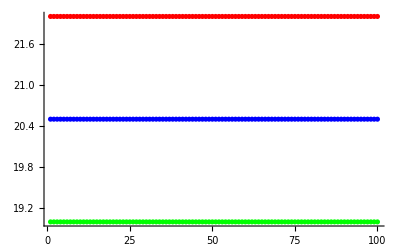

```mathematica
(*Determining the degree sequence of Ramsey Graphs*)
MaxD=T;MinD=T; AvD=T;V = Table[1, n];
For[i=1, i<= Len, i++,
Degreeseq = AdjacencyMatrix[G[[i]]].V;
MaxD[[i]] = Max[Degreeseq];
MinD[[i]]=Min[Degreeseq];
AvD[[i]]=(n-1)/2
]
Show[{ListPlot[MaxD, PlotStyle->Red], ListPlot[MinD, PlotStyle->Green], ListPlot[AvD, PlotStyle-> Blue]}, PlotRange->All]
```